```mathematica
fileName = "/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json";
RadioButtonBar[
Dynamic[fileName],
{
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json",
"~/Downloads/optimizerHistory.json"
},Appearance->"Vertical"]
```

| /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json
 | ~/Downloads/optimizerHistory.json

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

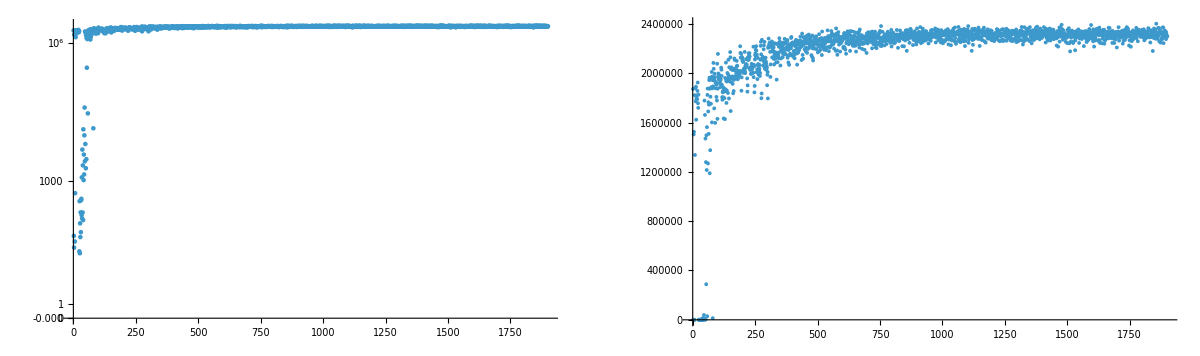

```mathematica
GraphicsGrid[{{
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600,
ScalingFunctions->"SignedLog"
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

L1PhaseSet : -26.5133471429
L2PhaseSet : -39.3450450004
Q1EkG : 113.7850217773
Q2EkG : -152.1836013016
Q3EkG : 128.5244553522
Q4EkG : 95.6005938793
Q5EkG : -2.7789318034
Q6EkG : -151.6349336035
S1ELkG : 759.4781617899
S2ELkG : -4671.4413087484
S3ELkG : -1104.8281641308
S3ERkG : -1401.6671360413
S2ERkG : -9677.5744584085
S1ERkG : 702.5864833881
S1EL_xOffset : -0.0006054483
S1EL_yOffset : -0.0006602461
S2EL_xOffset : 0.0006730135
S2EL_yOffset : -0.0004134554
S2ER_xOffset : 0.0004443489
S2ER_yOffset : 0.0001638508
S1ER_xOffset : -0.0019311703
S1ER_yOffset : -0.0002912521
PDrive_median_x : -5.1044e-6
PDrive_median_y : -2.2965e-6
PDrive_median_xp : -2.9907e-6
PDrive_median_yp : -1.326e-6
PDrive_sigmaSI90_x : 0.0000469162
PDrive_sigmaSI90_y : 0.0000107218
PDrive_sigmaSI90_z : 4.0264e-6
PDrive_sigmaSI90_xp : 0.0000496593
PDrive_sigmaSI90_yp : 0.0000237163
PDrive_emitSI90_x : 0.00003939
PDrive_emitSI90_y : 4.8469e-6
PDrive_norm_emit_x : 0.0000274319
PDrive_norm_emit_y : 2.2674e-6
PDrive_charge_nC : 1.6
PDrive_BMAG_x : 1.4159069213
PDrive_BMAG_y : 1.0075754388
PDrive_sliced_BMAG_x : List(2.2327278905,2.3663839765,3.9735687014,2.8375256348,1.7327050584)
PDrive_sliced_BMAG_y : List(1.0644914298,1.0984690462,1.3291890179,1.0840235269,1.3647537174)
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.
errorTerm_secondaryObjective : 3.3319e-6
maximizeMe : 2.4010635323183723e6
inputBeamFilePathSuffix : "/beams/2024-10-22_Impact_OneBunch/2024-10-22_oneBunch.h5"
csrTF : True

## Plot specific

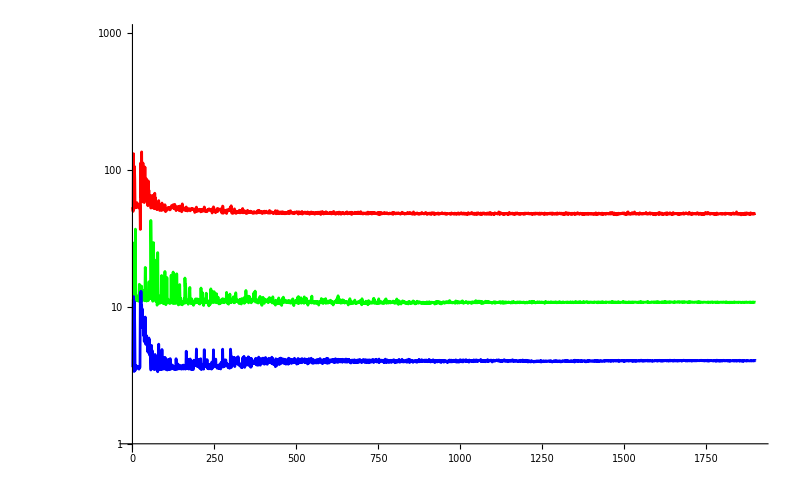

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{1,1000}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

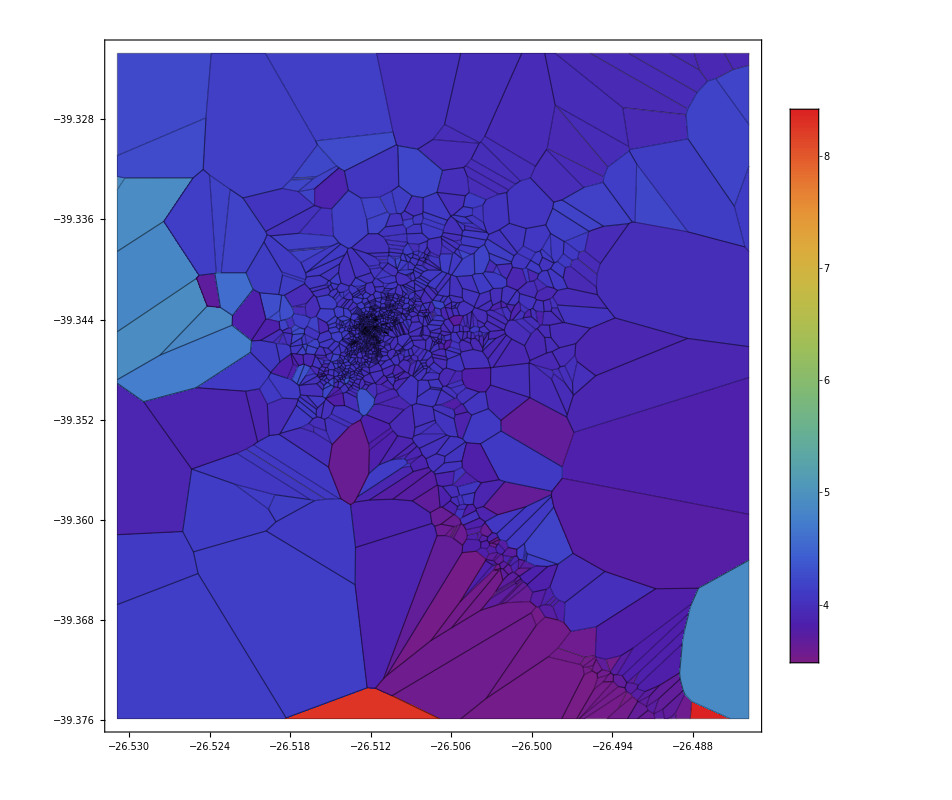

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

## Plot all

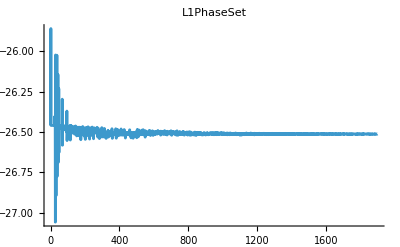
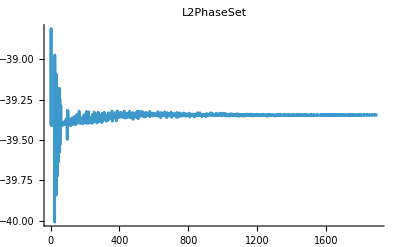
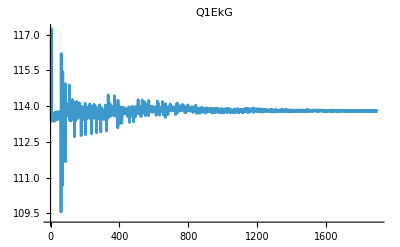
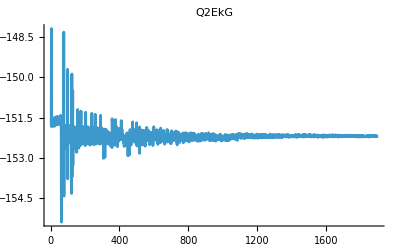
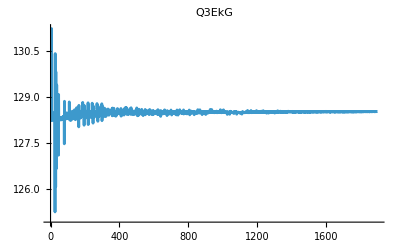
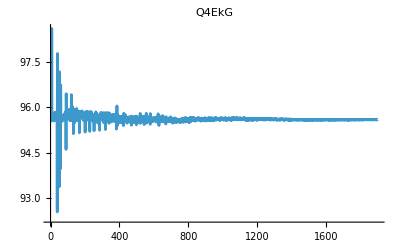
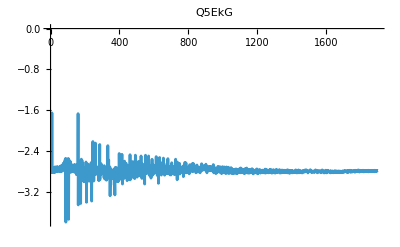
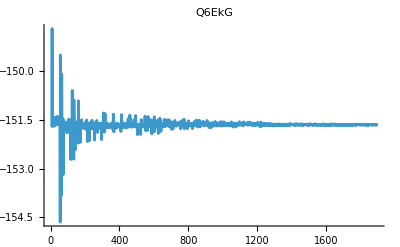
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | 0 | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,Q1EkG,Q2EkG,Q3EkG,Q4EkG,Q5EkG,Q6EkG,S1ELkG,S1EL_xOffset,S1EL_yOffset,S1ERkG,S1ER_xOffset,S1ER_yOffset,S2ELkG,S2EL_xOffset,S2EL_yOffset,S2ERkG,S2ER_xOffset,S2ER_yOffset,S3ELkG,S3ERkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | -26.5133 | -6.2013
L2PhaseSet | -38.6737 | -39.345 | -0.671339
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | -0.000605448 | -0.000990703
S1EL_yOffset | -0.000241114 | -0.000660246 | -0.000419132
S2EL_xOffset | -0.00141787 | 0.000673014 | 0.00209088
S2EL_yOffset | 0.0000111705 | -0.000413455 | -0.000424626
S2ER_xOffset | -0.00223816 | 0.000444349 | 0.00268251
S2ER_yOffset | -0.000675996 | 0.000163851 | 0.000839847
S1ER_xOffset | 0.00100714 | -0.00193117 | -0.00293831
S1ER_yOffset | 0.000398456 | -0.000291252 | -0.000689708
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]